```mathematica
e= 1.602 * 10^-19;
c = 2.998 * 10^8;
m =0.911 * 10^-30;
h = 6.626 * 10^-34;
Subscript[C, 1] = (h *10^10)/(√(2 m e 10^3))
Subscript[C, 2]= (e 10^3)/(2 m c^2)
V = {30, 37, 47, 61, 83, 120};
set = 1/(√(#(1 + Subscript[C, 2] #))) &/@ V
λ=Subscript[C, 1] # & /@ set
R2={38, 34, 30,26,22.5,19};
R3={45.5,41,36,32,27,23};
(*Show[ListLinePlot[{R2, set},Mesh->Full],ListLinePlot[{R3, set},Mesh->Full],PlotRange->{{0,7},{15,50}},AxesOrigin->{0,15}]*)
```

0.387834

0.000978252

{0.179953,0.161502,0.142623,0.12438,0.105562,0.0863589}

{0.0697918,0.062636,0.0553141,0.0482386,0.0409407,0.0334929}

```mathematica
pl1 = {};
For[i = 1, i ≤ Length[R2], i++, AppendTo[pl1, {set[[i]],R2[[i]]}]];
pl2 = {};
For[i = 1, i ≤ Length[R3], i++, AppendTo[pl2, {set[[i]],R3[[i]]}]];
```

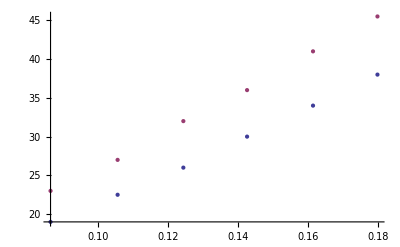

```mathematica
ListPlot[{pl1,pl2}]
```

{{Log[50]/Log[10],0.308},{2,0.357},{Log[150]/Log[10],0.435},{Log[200]/Log[10],0.483},{Log[250]/Log[10],0.466},{Log[300]/Log[10],0.46},{Log[350]/Log[10],0.427},{Log[400]/Log[10],0.426},{Log[450]/Log[10],0.415},{Log[500]/Log[10],0.404},{Log[550]/Log[10],0.383},{Log[600]/Log[10],0.382},{Log[650]/Log[10],0.368},{Log[700]/Log[10],0.374},{Log[750]/Log[10],0.368},{Log[800]/Log[10],0.365},{Log[850]/Log[10],0.373},{Log[900]/Log[10],0.38},{Log[950]/Log[10],0.385},{3,0.382}}

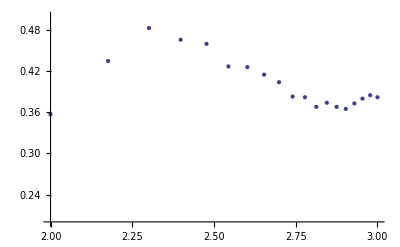

```mathematica
k1 = {0.308, 0.357, 0.435, 0.483, 0.466, 0.46, 0.427, 0.426, 0.415, 0.404, 0.383, 0.382, 0.368, 0.374, 0.368, 0.365, 0.373, 0.38, 0.385, 0.382};
k = {50, 100, 150, 200, 250, 300, 350, 400, 450, 500, 550, 600, 650, 700, 750, 800, 850, 900, 950,1000};
pl= {};
For[j = 1, j ≤ Length[k], j++,  AppendTo[pl, {Log[10, k[[j]]], k1[[j]]}]];
pl
ListPlot[pl, PlotRange->{{2, 3},{0.2, 0.5}}]
```

```mathematica
Log
```

{{Log[50]/Log[10],0.308},{2,0.357},{Log[150]/Log[10],0.435},{Log[200]/Log[10],0.483},{Log[250]/Log[10],0.466},{Log[300]/Log[10],0.46},{Log[350]/Log[10],0.427},{Log[400]/Log[10],0.426},{Log[450]/Log[10],0.415},{Log[500]/Log[10],0.404},{Log[550]/Log[10],0.383},{Log[600]/Log[10],0.382},{Log[650]/Log[10],0.368},{Log[700]/Log[10],0.374},{Log[750]/Log[10],0.368},{Log[800]/Log[10],0.365},{Log[850]/Log[10],0.373},{Log[900]/Log[10],0.38},{Log[950]/Log[10],0.385},{3,0.382}}

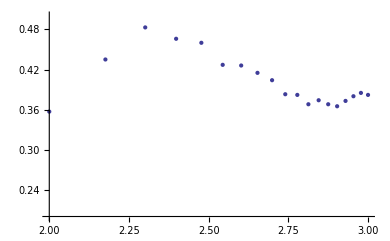
2 -Graphics-

```mathematica
k5 = {0, 0.036, 0.065, 0.05, 0.55,0.069, 0.087,0.087,0.085, 0.078, 0.071, 0.067, 0.066,0.067, 0.077, 0.081, 0.077, 0.073, 0.07, 0.074 };
k = {50, 100, 150, 200, 250, 300, 350, 400, 450, 500, 550, 600, 650, 700, 750, 800, 850, 900, 950,1000};
pl2= {};
For[j = 1, j ≤ Length[k], j++,  AppendTo[pl2, {Log[10, k[[j]]], k5[[j]]}]];
pl
ListPlot[pl, PlotRange->{{2, 3},{0.2, 0.5}}]2
```